```mathematica
Import["https://qtechtheory.org/questlink.m"];
CreateDownloadedQuESTEnv[];
```

# What is a Device Specification?

A device specification is an Association with specific keys, which represents a realistic hardware device. It describes the gate and qubit constraints of the device, how long gates take to apply, the noise channels induced by imperfect attempts to perform each gate, and the passive noise channels on inactive qubits. A device specification can be used to transform an ideal circuit description (one compatible with perfect state-vector simulation) into a schedule of gates, and/or a realistic noisy channel description (compatible with density matrix simulation).

# Creating Device Specifications

General tips for creating  a device specification:
	• View all available device spec fields using ?QuEST`DeviceSpec`*
	• Use CheckDeviceSpec[] to ensure a device spec has a valid structure
	• Use ViewDeviceSpec[] to view how the spec will be interpreted
	• Debug by inserting Echo statements into the RHS  of Gates entries, which trigger only when such a gate is encountered in a circuit.

Table of Contents (clickable):
	• Minimum Working Example
	• Gates and Active Noise
	• Passive Noise
	• Time Dependence
	• Aliases and Initialisations
	• Variables
	• Hidden Qubits

## Minimum Working Example

Here is the minimum boilerplate to specify a valid (but grossly uninteresting) device:

```mathematica
myDevSpec = <|

	(* A helpful description of the device *)
	DeviceDescription -> "A single beautiful qubit. No touching!",
	
	(* The number of logical qubits. This informs the qubits that a user's circuit can target *)
	NumAccessibleQubits -> 1,
	
	(* The total number of qubits which would be needed to simulate a circuit prescribed by this device.
	 * This is > numLogicQubits only when the spec uses hidden qubits for advanced noise modelling *)
	NumTotalQubits -> 1,
	
	(* The supported gates. This device supports none! *)
	Gates -> {},
	
	(* The passive noise on qubits when not being operated upon. This device suffers none! *)
	Qubits -> {}
|>;
```

Since this spec doesn’t include any gate descriptions, it permits no gates acting on any qubits!

```mathematica
InsertCircuitNoise[  Circuit[Subscript[X, 0] Subscript[Y, 0]], myDevSpec]
```

InsertCircuitNoise::error: The given subcircuits contain gates not supported by the given device specification. See ?GetUnsupportedGates.

$Failed

```mathematica
GetUnsupportedGates[ Circuit[Subscript[X, 0] Subscript[Y, 0]], myDevSpec]
```

{X_0,Y_0}

## Gates and Active Noise

Let’s make some gates possible on the device, and describe their noisy forms. 
The syntax of a supported gate is :

```mathematica
gatePattern :> <|
		NoisyForm -> Circuit[ operators ],
		GateDuration -> duration
	|>
```

When processing a user’s circuit (in functions like InsertCircuitNoise), gates which satisfy gatePattern will be replaced with the specified operators in the NoisyForm.

A simple gatePattern can specify a supported gate precisely, like a T gate on strictly the first qubit:

```mathematica
Subscript[T, 0] :>
```

or leave features of the gate general, like target qubit and parameter:

```mathematica
Subscript[Rz, q_][θ_] :>
```

The gatePattern can use the full power of Mathematica’s pattern matching to describe supported gates, including constraints! The below pattern matches only c-Pauli gates which control on one of the first three qubits, target only the higher qubits, and where the involved qubits are non-adjacent!

```mathematica
Subscript[C, c_ /; c < 3][Subscript[(X|Y|Z), q_ /; q ≥ 3]] /; (Abs[q-c] ≥ 2) :>
```

Notice that constraints should be in brackets, to not confuse Mathematica’s order of evaluation in complicated patterns.

The NoisyForm circuit is a sequence of operators which will replace the gatePattern in a user’s input circuit. It can include named sub-patterns in gatePattern (as can GateDuration).
For example, one can specify that a T gate on any qubit is performed perfectly:

```mathematica
Subscript[T, q_] :> <|  NoisyForm -> Circuit[Subscript[T, q]] |>
```

or that the gate invokes both pre and post noisy channels:

```mathematica
Subscript[T, q_] :> <|  NoisyForm -> Circuit[  Subscript[Deph, q][.1]  Subscript[T, 0]  Subscript[Depol, q][.1] ] |>
```

or has a noisy form not even expressed in terms of the perfect gate:

```mathematica
Subscript[T, q_] :> <|  NoisyForm -> Circuit[ Subscript[Rz, q][π/2 + .1] ] |>
```

or even that the gate interferes with other qubits, such as via cross-talk on neighbouring qubits:

```mathematica
Subscript[T, q_] :> <|  NoisyForm -> Circuit[ Subscript[T, q] Subscript[Depol, q,q-1][.1] Subscript[Depol, q,q+1][.1] ] |>
```

Note that controlled gates like C_0[T_1] are treated entirely separate from their uncontrolled forms in gatePattern.
Note too that general-matrix gates like U[{{...}}] should not appear in gatePattern, but instead be specified via an Alias.

Here’s an updated device spec:

```mathematica
myDevSpec = <|
	DeviceDescription -> "A line of 5 nearest-neighbour perfect qubits, with imperfect gates",
	NumAccessibleQubits -> 5,
	NumTotalQubits -> 5,
	
	Gates -> {
	
		(* Allow an Rx gate on any target qubit q *)
		Subscript[Rx, q_][θ_] :> <|
			(* Its noisy form includes a small over-rotation on the same qubit*) 
			NoisyForm -> Circuit[ Subscript[Rx, q][θ + π/10] ],
			
			(* The (dimensionless) duration to perform the gate is depends on θ *)
			GateDuration -> Abs[θ]/(2π)
		|>,
		
		(* Allow only nearest-neighbour CNOTs, but left qubit cannot be controlled *)
		Subscript[C, c_/;(c=!=0)][Subscript[X, q_]] /; (Abs[q-c] === 1) :> <|
		
			(* Its noisy form depolarises the control and target qubits *)
			NoisyForm -> Circuit[ Subscript[C, c][Subscript[X, q]] Subscript[Depol, c,q][.01] ],
			
			(* The higher index qubits are slower to target *)
			GateDuration -> 1 + q
		|>
	},
	
	(* This device also experiences no passive noise *)
	Qubits -> {}
|>;
```

```mathematica
ViewDeviceSpec[myDevSpec]
```

Fields | 
Number of accessible qubits | 5
Number of hidden qubits | 0
Number of qubits (total) | 5
Description | A line of 5 nearest-neighbour perfect qubits, with imperfect gates
Gates |  |  | 
Gate | Conditions | Noisy form | Duration
Rx_q_[θ_] |  | Rx_q[π/10+θ] | Abs[θ]/(2 π)
C_c_[X_q_] | c=!=0
Abs[q-c]===1 | C_c[X_q]
Depol_(c,q)[0.01] | 1+q
Qubits | 
Qubit | Passive noise
0 | 
1 | 
2 | 
3 | 
4 |

This device allows only Rx gates (prescribing over-rotations), or CNOTs on adjacent qubits (prescribing de-polarising noise)

```mathematica
in = Circuit[ Subscript[Rx, 0][a]Subscript[Rx, 1][b]Subscript[Rx, 4][c]Subscript[C, 2][Subscript[X, 3]]];
sched = InsertCircuitNoise[in, myDevSpec];
ViewCircuitSchedule[sched]
DrawCircuit[sched]
```

time | active noise
0 | Rx_0[a+π/10]Rx_1[b+π/10]Rx_4[c+π/10]C_2[X_3]Depol_(2,3)[0.01]

-Graphics-

Other gates, and CNOTs on non-adjacent qubits, are not permitted on this device, since we didn’t specify them. We furthermore cannot apply supported gates to qubits which don’t exist!

```mathematica
in = Circuit[ Subscript[Ry, 0][a]Subscript[C, 2][Subscript[X, 4]] Subscript[Rx, 10][b]];
InsertCircuitNoise[in, myDevSpec]
GetUnsupportedGates[in, myDevSpec]
```

InsertCircuitNoise::error: The given subcircuits contain gates not supported by the given device specification. See ?GetUnsupportedGates.

$Failed

{Ry_0[a],C_2[X_4],Rx_10[b]}

Note that besides inserting noise, InsertCircuitNoise has also determined a schedule for the gates! This is inferred by splitting the circuit into sub-circuits of non-overlapping gates (via GetCircuitColumns[]), and assigning each sub-circuit’s duration to be the slowest gate therein.

time | active noise
0 | Rx_0[a+π/10]C_1[X_2]Depol_(1,2)[0.01]Rx_4[c+π/10]
Max[3,Abs[a]/(2 π),Abs[c]/(2 π)] | Rx_1[b+π/10]C_2[X_3]Depol_(2,3)[0.01]

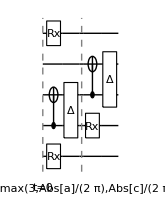

```mathematica
in =  Circuit[ Subscript[Rx, 0][a]Subscript[C, 1][Subscript[X, 2]]Subscript[Rx, 1][b]Subscript[Rx, 4][c]Subscript[C, 2][Subscript[X, 3]] ];
sched = InsertCircuitNoise[in, myDevSpec];
ViewCircuitSchedule[sched]
DrawCircuit[sched]
```

Notice that the gate durations can be symbolic (since the gate parameters were), and hence the schedule times and decoherence parameters can be analytic! It can be helpful to keep durations symbolic (e.g. as undefined symbols GateDuration → myGateDur[θ]) when creating a new device spec.

## Passive Noise

We use Gates → NoisyForm to describe the effect on qubits when gates are performed imperfectly. But what about the passive decoherence of qubits when idle due to imperfect isolation? To describe this, we use Qubits → PassiveNoise. PassiveNoise describes the noise channels on qubits in the periods for which they are not being acted upon by gates; for example, the period after the qubit was acted upon by a gate but before the next sub-circuit begins.

Let’s modify the previous example, so that idle qubits experience passive noise for the time they aren’t being operated upon in the inferred circuit schedule. The syntax of a Qubit spec is:

```mathematica
qubitIndexPattern :> <|
		PassiveNoise -> Circuit[ operators ]
	|>
```

where qubitIndexPattern is any pattern which matches one or more qubit index integers (e.g. _Integer), and operators are a passive noise channel effected on the qubits when idle. Every logical qubit index (from 0 to NumAccessibleQubits-1) will be attemptedly matched with one qubitIndexPattern, matching with the first found. If no match is found, that qubit is assumed unaffected by passive noise.

Any sensible description of passive noise will decohere qubits with strength proportional to the idle time. A PassiveNoise channel can access the duration of the channel through the symbol specified with optional device spec key DurationSymbol.
While a circuit is being processed, the specified DurationSymbol will have the duration of the current noise process substituted. We incorporate this into the example below.

```mathematica
(* Declare Δt a private symbol using Module[] *)
myDevSpec = Module[{Δt},
<|
	DeviceDescription -> "A line of 5 nearest-neighbour decohering qubits, with imperfect gates",
	NumAccessibleQubits -> 5,
	NumTotalQubits -> 5,

	Gates -> {
		Subscript[Rx, q_][θ_] :> <|
			NoisyForm -> Circuit[ Subscript[Rx, q][θ + π/10] ],
			GateDuration -> Abs[θ]/(2π)
		|>,
		Subscript[C, c_][Subscript[X, q_]] /; (Abs[q-c] === 1) :> <|
			NoisyForm -> Circuit[ Subscript[C, c][Subscript[X, q]] Subscript[Depol, c,q][.01] ],
			GateDuration -> 1 + q
		|>
	},
	
	(* Declare that Δt will refer to the duration of the current gate/channel. *)
	DurationSymbol -> Δt,
	
	Qubits -> {

		(* The central qubit (index 2) will depolarise, when idle for Δt *)
		2 :> <|
			PassiveNoise -> Circuit[ Subscript[Depol, 2][.5(1-ⅇ^-Δt)]]
		|>,

		(* The other qubits (except 3) dephase, with strength growing quadratically with qubit index! *)
		q_ /; (q =!= 3) :> <|
			PassiveNoise -> With[
				{f = (1+q)^2(1-ⅇ^-Δt)},
				Circuit[ Subscript[Deph, q][f] ]] 
		|>
	}
|>];
```

Note that the time symbol Δt was declared as a local symbol to the device spec, using Module[]. This is good practice, to avoid the symbol colliding with a  variable of the same name, declared in the same Context as the device spec.

```mathematica
ViewDeviceSpec[myDevSpec]
```

Fields | 
Number of accessible qubits | 5
Number of hidden qubits | 0
Number of qubits (total) | 5
Duration symbol | Δt
Description | A line of 5 nearest-neighbour decohering qubits, with imperfect gates
Gates |  |  | 
Gate | Conditions | Noisy form | Duration (Δt)
Rx_q_[θ_] |  | Rx_q[π/10+θ] | Abs[θ]/(2 π)
C_c_[X_q_] | Abs[q-c]===1 | C_c[X_q]
Depol_(c,q)[0.01] | 1+q
Qubits | 
Qubit | Passive noise
0 | Deph_0[1-ⅇ^-Δt]
1 | Deph_1[4 (1-ⅇ^-Δt)]
2 | Depol_2[0.5 (1-ⅇ^-Δt)]
3 | 
4 | Deph_4[25 (1-ⅇ^-Δt)]

The output noisy schedule now includes stages of passive noise of the qubits! Qubits are decohered for their remaining idle period in the scheduled subcircuit:

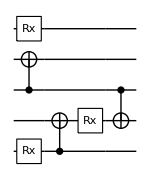

```mathematica
in =  Circuit[ Subscript[Rx, 0][.1]Subscript[C, 0][Subscript[X, 1]]Subscript[Rx, 1][.2]Subscript[Rx, 4][.3]Subscript[C, 2][Subscript[X, 3]] Subscript[C, 2][Subscript[X, 1]]];
DrawCircuit[in]
```

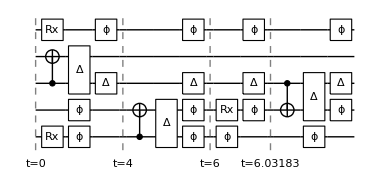

time | active noise | passive noise
0 | Rx_0[0.414159]Rx_4[0.614159]C_2[X_3]Depol_(2,3)[0.01] | Deph_0[0.981391]Deph_1[4 (1-1/ⅇ^4)]Depol_2[0.]Deph_4[24.5197]
4 | C_0[X_1]Depol_(0,1)[0.01] | Deph_0[0]Deph_1[0]Depol_2[0.432332]Deph_4[25 (1-1/ⅇ^2)]
6 | Rx_1[0.514159] | Deph_0[0.0313297]Deph_1[0.]Depol_2[0.0156649]Deph_4[0.783243]
6.03183 | C_2[X_1]Depol_(2,1)[0.01] | Deph_0[1-1/ⅇ^2]Deph_1[0]Depol_2[0.]Deph_4[25 (1-1/ⅇ^2)]

```mathematica
sched = InsertCircuitNoise[in, myDevSpec];
DrawCircuit[sched]
ViewCircuitSchedule[sched]
```

Notice how the strength of the passive noise depends on the duration for which qubits were idle after the gates acting on them in each subcircuit (while the slowest gate continued). Hence, in the first subcircuit, notice qubit 1 (no gates) was decohered for the full duration 4, while qubits 2 and 3 were occupied by the slowest gate C[X] for the full subcircuit (so decohered for duration 0).

As before, parameters, durations, times and noise strengths can be symbolic/analytic! In this scenario, the idle qubits aren’t even determined yet!

```mathematica
in =  Circuit[ Subscript[Rx, 0][a]Subscript[C, 0][Subscript[X, 1]]Subscript[Rx, 1][b]Subscript[Rx, 4][c]Subscript[C, 2][Subscript[X, 3]]];
InsertCircuitNoise[in, myDevSpec];
ViewCircuitSchedule[%]
```

time | active noise | passive noise
0 | Rx_0[a+π/10]Rx_4[c+π/10]C_2[X_3]Depol_(2,3)[0.01] | Deph_0[1-ⅇ^(Abs[a]/(2 π)-Max[4,Abs[a]/(2 π),Abs[c]/(2 π)])]Deph_1[4 (1-ⅇ^(-Max[4,Abs[a]/(2 π),Abs[c]/(2 π)]))]Depol_2[0.5 (1-ⅇ^(4-Max[4,Abs[a]/(2 π),Abs[c]/(2 π)]))]Deph_4[25 (1-ⅇ^(Abs[c]/(2 π)-Max[4,Abs[a]/(2 π),Abs[c]/(2 π)]))]
Max[4,Abs[a]/(2 π),Abs[c]/(2 π)] | C_0[X_1]Depol_(0,1)[0.01] | Deph_0[0]Deph_1[0]Depol_2[0.432332]Deph_4[25 (1-1/ⅇ^2)]
2+Max[4,Abs[a]/(2 π),Abs[c]/(2 π)] | Rx_1[b+π/10] | Deph_0[1-ⅇ^(-Abs[b]/(2 π))]Deph_1[0]Depol_2[0.5 (1-ⅇ^(-Abs[b]/(2 π)))]Deph_4[25 (1-ⅇ^(-Abs[b]/(2 π)))]

The specified DurationSymbol can also appear in the NoisyForm of Gates, where it’s a convenient concise reference to the duration of the gate (determined by GateDuration). For example, here’s a rotation gate which is actively dampened during its operation:

```mathematica
Subscript[Rx, q_][θ_] :> <|
			NoisyForm -> Circuit[ Subscript[Rx, q][θ ] Subscript[Damp, q][Δt] ],  (* Δt -> myComplicatedFunc[θ] *)
			GateDuration -> myComplicatedFunc[θ]
		|>
```

Obviously DurationSymbol cannot appear inside and hence determine a GateDuration!

```mathematica
myDevSpec /. {
(* rename duration symbol to (non-private) symbol dur *)
myDevSpec[DurationSymbol] -> dur, 
(* invadliy declare active gate durations as dur (a loop!) *)
(GateDuration -> _) -> (GateDuration -> dur)};

CheckDeviceSpec[%]
```

CheckDeviceSpec::error: A GateDuration cannot refer to the DurationSymbol, since the DurationSymbol is substituted the value of the former.

False

Concretely, the DurationSymbol will be substituted a value of:
	• a gate’s GateDuration, when featured in a gate’s NoisyForm circuit (as a matter of convenience).
	• the duration of idleness of a qubit, when featured in a qubit’s PassiveNoise circuit. 
	  This is the time remaining in the sub-circuit after the qubit’s active gates have completed (if any).
	  Note that if a qubit is idle for multiple contiguous sub-circuits, the PassiveNoise will be invoked for 
	  each sub-circuit with that sub-circuit’s duration (rather than once for the entire idle period). Hence a
	  realistic channel should be a “divisible channel” (a one-parameter group flow).

## Time Dependence

Similar to DurationSymbol, we can specify a TimeSymbol, creating a reference to the scheduled start-time of a gate or noise channel. This can be used by both NoisyForm and PassiveNoise circuits, and can even determine the duration of a gate (via GateDuration)! This allows global time-dependent noise, like might be caused by a changing qubit environment.

```mathematica
myDevSpec = Module[{t, Δt},
<|
	DeviceDescription -> "A line of qubits with progressively worsening and slowing gates. Better act quick!",
	NumAccessibleQubits -> 5,
	NumTotalQubits -> 5,
	
	TimeSymbol -> t,
	DurationSymbol -> Δt,

	Gates -> {
	
		Subscript[Rx, q_][θ_] :> <|

			(* Over-rotation increasing with time, and gate duration *)
			NoisyForm -> Circuit[ Subscript[Rx, q][θ + t Δt π/10] ],
			
			(* Meanwhile the gate slows down quadratically with time! *)
			GateDuration -> t^2 + Abs[θ]/(2π)
		|>,
		
		Subscript[C, c_][Subscript[X, q_]] /; (Abs[q-c] === 1) :> <|
		
			(* Active noise strength worsens in time *)
			NoisyForm -> Circuit[ Subscript[C, c][Subscript[X, q]] Subscript[Depol, c,q][.5 - .5(1-ⅇ^-t)] ],
			
			GateDuration -> 1 + q
		|>
	},
	
	Qubits -> {
		(* All passive noise depends both on start time of qubit idleness (in some exotic function f) 
		 * and the duration of qubit idleness (in some exotic function g) *)
		q_ :> <|
			PassiveNoise -> With[{μ = 3/10(1-ⅇ^(-f[t]-g[Δt]))}, Circuit[ Subscript[Deph, q][μ] ]]
		|>
	}
|>];
```

```mathematica
ViewDeviceSpec[myDevSpec]
```

Fields | 
Number of accessible qubits | 5
Number of hidden qubits | 0
Number of qubits (total) | 5
Time symbol | t
Duration symbol | Δt
Description | A line of qubits with progressively worsening and slowing gates. Better act quick!
Gates |  |  | 
Gate | Conditions | Noisy form | Duration (Δt)
Rx_q_[θ_] |  | Rx_q[(π t Δt)/10+θ] | t^2+Abs[θ]/(2 π)
C_c_[X_q_] | Abs[q-c]===1 | C_c[X_q]
Depol_(c,q)[0.5-0.5 (1-ⅇ^-t)] | 1+q
Qubits | 
Qubit | Passive noise
0 | Deph_0[3/10 (1-ⅇ^(-f[t]-g[Δt]))]
1 | Deph_1[3/10 (1-ⅇ^(-f[t]-g[Δt]))]
2 | Deph_2[3/10 (1-ⅇ^(-f[t]-g[Δt]))]
3 | Deph_3[3/10 (1-ⅇ^(-f[t]-g[Δt]))]
4 | Deph_4[3/10 (1-ⅇ^(-f[t]-g[Δt]))]

This can make the circuit schedule quite complicated!

```mathematica
in =  Circuit[ Subscript[Rx, 0][.1]Subscript[C, 0][Subscript[X, 1]]Subscript[Rx, 1][.2]Subscript[Rx, 3][-.1]Subscript[Rx, 4][.3]Subscript[C, 2][Subscript[X, 3]] Subscript[C, 4][Subscript[X, 3]] Subscript[C, 2][Subscript[X, 1]] ];
ViewCircuitSchedule @ InsertCircuitNoise[in, myDevSpec]
```

time | active noise | passive noise
0 | Rx_0[0.1]Rx_3[-0.1]Rx_4[0.3] | Deph_0[3/10 (1-ⅇ^(-f[0.0159155]-g[0.031831]))]Deph_1[3/10 (1-ⅇ^(-f[0]-g[0.0477465]))]Deph_2[3/10 (1-ⅇ^(-f[0]-g[0.0477465]))]Deph_3[3/10 (1-ⅇ^(-f[0.0159155]-g[0.031831]))]Deph_4[3/10 (1-ⅇ^(-f[0.0477465]-g[0.]))]
0.0477465 | C_0[X_1]Depol_(0,1)[0.476688]C_2[X_3]Depol_(2,3)[0.476688] | Deph_0[3/10 (1-ⅇ^(-f[2.04775]-g[2]))]Deph_1[3/10 (1-ⅇ^(-f[2.04775]-g[2]))]Deph_2[3/10 (1-ⅇ^(-f[4.04775]-g[0]))]Deph_3[3/10 (1-ⅇ^(-f[4.04775]-g[0]))]Deph_4[3/10 (1-ⅇ^(-f[0.0477465]-g[4]))]
4.04775 | Rx_1[21.0753]C_4[X_3]Depol_(4,3)[0.00873084] | Deph_0[3/10 (1-ⅇ^(-f[4.04775]-g[16.4161]))]Deph_1[3/10 (1-ⅇ^(-f[20.4638]-g[0.]))]Deph_2[3/10 (1-ⅇ^(-f[4.04775]-g[16.4161]))]Deph_3[3/10 (1-ⅇ^(-f[8.04775]-g[12.4161]))]Deph_4[3/10 (1-ⅇ^(-f[8.04775]-g[12.4161]))]
20.4638 | C_2[X_1]Depol_(2,1)[6.481×10^-10] | Deph_0[3/10 (1-ⅇ^(-f[20.4638]-g[2]))]Deph_1[3/10 (1-ⅇ^(-f[22.4638]-g[0]))]Deph_2[3/10 (1-ⅇ^(-f[22.4638]-g[0]))]Deph_3[3/10 (1-ⅇ^(-f[20.4638]-g[2]))]Deph_4[3/10 (1-ⅇ^(-f[20.4638]-g[2]))]

Concretely, the TimeSymbol will be substituted a value of:
	• the start time of the containing sub-circuit, when featured in a gate’s NoisyForm circuit.
	• the start time of idleness of a qubit, when featured in a qubit’s PassiveNoise circuit. 
	  This is either the end time of the qubit’s active gate in the sub-circuit (if it exists), else it’s the
	  start time of the sub-circuit (meaning the qubit is idle the entire sub-circuit).

## Aliases and Initialisations

Some real hardware devices can perform operations which aren’t described by a single canonical  “named” gate. These may be instead described by general matrices, or by a sequence of canonical gates or channels. Such custom gates may include qubit initialisation strategies. We can refer to such a gate in our device spec via a custom alias, and make its definition known to users of a device spec by describing it in the device’s list of Aliases.

An alias has the format:

```mathematica
gatePattern :> Circuit[ operators ]
```

where gatePattern should be an unconstrained gate pattern (using custom symbols), like:

```mathematica
Subscript[MyGate, q_] :> Circuit[ Subscript[X, q] Subscript[Y, q] Subscript[Z, q] ]
```

Aliases can include parameters:

```mathematica
Subscript[SpecialSWAP, a_,b_][θ_,ϕ_] :> Circuit[ Subscript[SWAP, a,b] Subscript[C, a][Subscript[U, b][ⅇ^(ⅈ ϕ)/(√2)({{1, ⅇ^(ⅈ θ)}, {ⅇ^(-ⅈ θ), -1}})]] Subscript[SWAP, a,b] ]
```

Concretely, the gatePattern should be any form which, when the qubit indices are given integer values, has the standard QuESTlink gate format of subscripted indices before optional square braces of parameters.

Aliased gates can then feature in the left-hand-side of Gates (as a supported gate), or in NoisyForm and PassiveNoise operators. Alias definitions can even include other aliases! (watch out for loops!)

```mathematica
myDevSpec = Module[{Δt},
<|
	DeviceDescription -> "Five qubits with some funky custom gates.",
	NumAccessibleQubits -> 5,
	NumTotalQubits -> 5,
	
	Aliases -> {
		(* Supported gates with a general matrix description must be aliased *)
		Subscript[A, q_][θ_] :> Circuit[ Subscript[U, q][1/(√2)({{ⅇ^(-ⅈ θ) (Cos[θ]-Sin[θ]), Cos[θ]+Sin[θ]}, {Cos[θ]+Sin[θ], ⅇ^(ⅈ θ) (-Cos[θ]+Sin[θ])}})] ],
		
		(* Aliases can resolve to a sequence of gates, including other aliases *)
		Subscript[B, q1_,q2_] :> Circuit[ Subscript[A, q1][π/3] Subscript[A, q2][π/3] Subscript[SWAP, q1,q2] Subscript[A, q1][-π/3] Subscript[A, q2][-π/3] ],
		
		(* Aliases are useful for declaring qubit preparations (here, set a qubit to + *)
		Subscript[Init, q_] :> Circuit[ Subscript[Damp, q][1] Subscript[H, q] ]
	},

	Gates -> {
		(* Allow A gates only on even-index qubits, with parameter ≤ π/3 *)
		Subscript[A, q_][θ_ /; θ ≤ π/3] /; ( EvenQ[q] ) :> <|
			NoisyForm -> Circuit[ Subscript[A, q][θ] Subscript[Damp, q][θ/100] ],
			GateDuration -> 1
		|>,
		
		(* Allow B gates only on pairs of odd and even qubit indices *)
		Subscript[B, q1_,q2_] /; ( OddQ @ Abs[q1-q2] ) :> <|
			NoisyForm -> Circuit[ Subscript[A, q1][π/10] Subscript[Depol, q1,q2][.1] Subscript[B, q1,q2]  ],
			GateDuration -> 1
		|>,
		
		(* Allow perfect qubit initialisation *)
		Subscript[Init, q_] :> <|
			NoisyForm -> Circuit[ Subscript[Init, q] ],
			GateDuration -> 1
		|>
	},
	
	DurationSymbol -> Δt,
	Qubits -> {
		q_ :> <|
			(* idle qubits dephase and "get A'd" depending on duration *)
			PassiveNoise -> Circuit[ Subscript[Deph, q][Δt] Subscript[A, q][Δt] ]
		|>
	}
|>];
```

```mathematica
ViewDeviceSpec[myDevSpec]
```

Fields | 
Number of accessible qubits | 5
Number of hidden qubits | 0
Number of qubits (total) | 5
Duration symbol | Δt
Description | Five qubits with some funky custom gates.
Aliases | 
Operator | Definition
A_q_[θ_] | U_q[((ⅇ^(-ⅈ θ) (Cos[θ]-Sin[θ]))/(√2) | (Cos[θ]+Sin[θ])/(√2)
(Cos[θ]+Sin[θ])/(√2) | (ⅇ^(ⅈ θ) (-Cos[θ]+Sin[θ]))/(√2))]
B_(q1_,q2_) | A_q1[π/3]A_q2[π/3]SWAP_(q1,q2)A_q1[-π/3]A_q2[-π/3]
Init_q_ | Damp_q[1]H_q
Gates |  |  | 
Gate | Conditions | Noisy form | Duration (Δt)
A_q_[θ_] | θ≤π/3
EvenQ[q] | A_q[θ]
Damp_q[θ/100] | 1
B_(q1_,q2_) | OddQ[Abs[q1-q2]] | A_q1[π/10]
Depol_(q1,q2)[0.1]
B_(q1,q2) | 1
Init_q_ |  | Init_q | 1
Qubits | 
Qubit | Passive noise
0 | Deph_0[Δt]
A_0[Δt]
1 | Deph_1[Δt]
A_1[Δt]
2 | Deph_2[Δt]
A_2[Δt]
3 | Deph_3[Δt]
A_3[Δt]
4 | Deph_4[Δt]
A_4[Δt]

A user’s input circuit can contain any aliases which have been specified as supported in Gates.

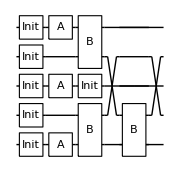

```mathematica
in = Circuit[ Subscript[Init, 0] Subscript[Init, 1] Subscript[Init, 2] Subscript[Init, 3] Subscript[Init, 4] Subscript[A, 0][.1]Subscript[A, 2][.2] Subscript[A, 4][.3] Subscript[B, 0,1] Subscript[Init, 2] Subscript[B, 3,4] Subscript[B, 0,3]];
DrawCircuit[in]
```

time | active noise | passive noise
0 | Init_0Init_1Init_2Init_3Init_4 | Deph_0[0]A_0[0]Deph_1[0]A_1[0]Deph_2[0]A_2[0]Deph_3[0]A_3[0]Deph_4[0]A_4[0]
1 | A_0[0.1]Damp_0[0.001]A_2[0.2]Damp_2[0.002]A_4[0.3]Damp_4[0.003] | Deph_0[0]A_0[0]Deph_1[1]A_1[1]Deph_2[0]A_2[0]Deph_3[1]A_3[1]Deph_4[0]A_4[0]
2 | A_0[π/10]Depol_(0,1)[0.1]B_(0,1)Init_2A_3[π/10]Depol_(3,4)[0.1]B_(3,4) | Deph_0[0]A_0[0]Deph_1[0]A_1[0]Deph_2[0]A_2[0]Deph_3[0]A_3[0]Deph_4[0]A_4[0]
3 | A_0[π/10]Depol_(0,3)[0.1]B_(0,3) | Deph_0[0]A_0[0]Deph_1[1]A_1[1]Deph_2[1]A_2[1]Deph_3[0]A_3[0]Deph_4[1]A_4[1]

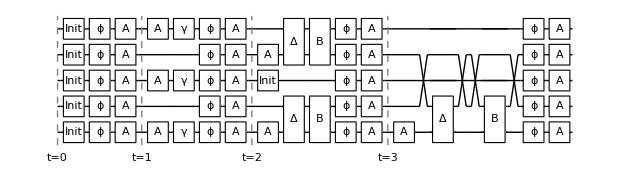

```mathematica
sched = InsertCircuitNoise[in, myDevSpec];
ViewCircuitSchedule[sched]
DrawCircuit[sched]
```

Notice that the aliases gates remain in the output circuit. We can substitute them for their definitions by using ReplaceAliases:

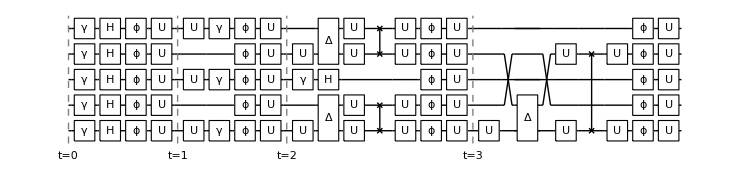

```mathematica
DrawCircuit @  InsertCircuitNoise[in, myDevSpec, ReplaceAliases -> True]
```

Aliases have several caveats:
	• Aliased gates are not assumed supported by the device. 
	  They must be explicitly included in Gates if intended to appear in user input circuits.
	• An alias definition should avoid including information about the device, like qubit constraints or noise; 
	  such information be specified in Gates. Strictly, alias definition should not include any constraints, 
	  such as on parameter values or on qubit indices.
	• Alias definitions must not depend on TimeSymbol or DurationSymbol directly. Instead, time and duration,
	  as accessed by NoisyForm and PassiveNoise, can be passed as parameters to an alias. 
	• The circuit variables introduced in the next section must also not appear in Aliases directly.

## Variables

So far, we have seen methods for specifying noise of a gate which is independent of other gates in the circuit, except through their influence on the circuit schedule. We now introduce circuit variables, which are variables updated through the processing of a circuit. These variables can track of anything, and determine noise and gate durations.

Variables should be declared first in a Module[] around the device spec, to keep them privately scoped.
Every variable should be set to their initial values inside a zero-argument anonymous function, with key InitVariables.
InitVariables is called before processing a circuit, in functions like InsertCircuitNoise and GetCircuitSchedule.

```mathematica
InitVariables -> Function[ i=0.1 ]
```

Every NoisyForm, PassiveNoise and GateDuration can refer to a variable, which will have substituted its current value during the circuit processing.

```mathematica
NoisyForm -> Circuit[ Subscript[Deph, 0][ i ] ]
```

The variables can be updated strictly after each processed gate, or passive noise, via UpdateVariables (another zero-argument anonymous function):

```mathematica
gatePattern :> <|
		UpdateVariables -> Function[ i++ ]
	|>
```

The function can make reference to the gatePattern. This means variables can be updated based on information about the current gate!

```mathematica
Subscript[Rx, q_][θ_] :> <|
		UpdateVariables -> Function[ i += q/θ ]
	|>
```

Here’s a simple and strange device where the number of performed T gates so far influences the noise of future T gates, and the duration of future Rx gates.

```mathematica
(* variables should be kept private to device spec, using Module[] *)
myDevSpec = Module[{numT},
<|
	DeviceDescription -> "Strange device where T gates 'warm' qubits, and slowdown subsequent Rx gates.",
	NumAccessibleQubits -> 5,
	NumTotalQubits -> 5,
	
	(* Resets circuit variables *)
	InitVariables -> Function[ numT = 0 ],

	Gates -> {
		Subscript[T, q_] :> <|
			(* let T noise depend on number of T gates so far, via some function f *)
			NoisyForm -> Circuit[ Subscript[T, q] Subscript[Deph, q][ f[numT] ] ],
			GateDuration -> 1,
			(* update the T gate count after processing this one *)
			UpdateVariables -> Function[ numT++ ]
		|>,
		
		Subscript[Rx, q_][θ_] :> <|
			NoisyForm -> Circuit[ Subscript[Rx, q][θ] ],
			(* let the duration of Rx gates depend on the number of prior T gates
			 * (including in the current subcircuit, as processed so far) *)
			GateDuration -> g[numT]
		|>
	},
	
	(* no passive noise *)
	Qubits -> {}
|>];
```

```mathematica
in = Circuit[Subscript[T, 0] Subscript[T, 1] Subscript[T, 2] Subscript[T, 3] Subscript[T, 2] Subscript[Rx, 0][.1]Subscript[Rx, 3][.1] Subscript[T, 1] Subscript[T, 2] Subscript[T, 3] Subscript[T, 2] Subscript[Rx, 3][.1] Subscript[T, 1] Subscript[T, 2] Subscript[T, 3]];
ViewCircuitSchedule @ InsertCircuitNoise[in, myDevSpec]
```

time | active noise
0 | T_0Deph_0[f[0]]T_1Deph_1[f[1]]T_2Deph_2[f[2]]T_3Deph_3[f[3]]
1 | T_2Deph_2[f[4]]Rx_0[0.1]Rx_3[0.1]T_1Deph_1[f[5]]
1+Max[1,g[5]] | T_2Deph_2[f[6]]T_3Deph_3[f[7]]T_1Deph_1[f[8]]
2+Max[1,g[5]] | T_2Deph_2[f[9]]Rx_3[0.1]
2+Max[1,g[5]]+Max[1,g[10]] | T_2Deph_2[f[10]]T_3Deph_3[f[11]]

Variables need not be scalars; they can be any Mathematica data-type (for example, a per-qubit list of properties).
Furthermore, UpdateVariables can even make use of the TimeSymbol and DurationSymbol, which will be substituted with their values at the time the gate or channel is processed (like NoisyForm). 
Here is a sophisticated example of a very strangely behaving device:

```mathematica
myDevSpec = Module[{
	Δt, 
	totalRotation, totalIdleTime, numGatesOnQubit
}, <|
	DeviceDescription -> "Whacky device where Rx slow themselves down, idle qubits ruin T gates, and gates ruin idle qubits.",
	NumAccessibleQubits -> 5,
	NumTotalQubits -> 5,
	
	InitVariables -> Function[
		totalRotation = 0;
		totalIdleTime = 0;
		numGatesOnQubit = ConstantArray[0, 5];
	],

	Gates -> {
		Subscript[T, q_] :> <|
			(* Dephase target qubit based on total cumulative idle time of all qubits so far *)
			NoisyForm -> Circuit[ Subscript[T, q] Subscript[Deph, q][totalIdleTime] ],
			GateDuration -> 1,
			UpdateVariables -> Function[ numGatesOnQubit⟦q+1⟧ ++ ]
		|>,
		Subscript[Rx, q_][θ_] :> <|
			(* Slow Rx by total rotation so far *)
			NoisyForm -> Circuit[ Subscript[Rx, q][θ] ],
			GateDuration -> totalRotation,
			UpdateVariables -> Function[
				totalRotation += Abs[θ];
				numGatesOnQubit⟦q+1⟧ ++
			]
		|>
	},
	
	DurationSymbol -> Δt,
	Qubits -> {
		q_ :> <|
			(* Dampen idle qubit based on the number of gates applied to it so far *)
			PassiveNoise -> Circuit[ Subscript[Deph, q][ numGatesOnQubit⟦q+1⟧ ] ],
			UpdateVariables -> Function[
				totalIdleTime += Δt
			]
		|>
	}
|>];
```

```mathematica
in = Circuit[Subscript[T, 0] Subscript[T, 1] Subscript[T, 2] Subscript[T, 3] Subscript[T, 2] Subscript[Rx, 0][a]Subscript[Rx, 3][b] Subscript[T, 1] Subscript[T, 2] Subscript[T, 3] Subscript[T, 2] Subscript[Rx, 3][c] Subscript[T, 1] Subscript[T, 2] Subscript[T, 3]];
ViewCircuitSchedule @ InsertCircuitNoise[in, myDevSpec]
```

time | active noise | passive noise
0 | T_0Deph_0[0]T_1Deph_1[0]T_2Deph_2[0]T_3Deph_3[0] | Deph_0[1]Deph_1[1]Deph_2[1]Deph_3[1]Deph_4[0]
1 | T_2Deph_2[1]Rx_0[a]Rx_3[b]T_1Deph_1[1] | Deph_0[2]Deph_1[2]Deph_2[2]Deph_3[2]Deph_4[0]
1+Max[1,Abs[a]] | T_2Deph_2[-1-Abs[a]+5 Max[1,Abs[a]]]T_3Deph_3[-1-Abs[a]+5 Max[1,Abs[a]]]T_1Deph_1[-1-Abs[a]+5 Max[1,Abs[a]]] | Deph_0[2]Deph_1[3]Deph_2[3]Deph_3[3]Deph_4[0]
2+Max[1,Abs[a]] | T_2Deph_2[1-Abs[a]+5 Max[1,Abs[a]]]Rx_3[c] | Deph_0[2]Deph_1[3]Deph_2[4]Deph_3[4]Deph_4[0]
2+Max[1,Abs[a]]+Max[1,Abs[a]+Abs[b]] | T_2Deph_2[-2 Abs[a]-Abs[b]+5 Max[1,Abs[a]]+5 Max[1,Abs[a]+Abs[b]]]T_3Deph_3[-2 Abs[a]-Abs[b]+5 Max[1,Abs[a]]+5 Max[1,Abs[a]+Abs[b]]] | Deph_0[2]Deph_1[3]Deph_2[5]Deph_3[5]Deph_4[0]

UpdateVariables can also appear in a Qubits entry in the same way, triggered after a qubit’s passive noise is determined.

Since gate durations and the subsequent schedule can depend on variables as they update, it is important to understand the order of evaluation. In a function like InsertCircuitNoise[], the evaluation follows:

• split circuit into sub-circuits of non-overlapping gates (via GetCircuitColumns[])
• invoke InitVariables[]
• for each sub-circuit:
	• for each gate in sub-circuit:
		• determine the NoisyForm and GateDuration via the current variables
		•  invoke the gate’s UpdateVariables[], if exists
	•  infer the sub-circuit duration via the slowest gate (may be overridden by forced user schedule)
	•  for each qubit in {0, ..., NumAccessibleQubits-1}:
		• determine the PassiveNoise via the current variables
		•  invoke the qubit’s UpdateVariables[], if exists
		
It is important to keep in mind that the gates within a sub-circuit are not necessarily ordered by the qubits they target, nor by the order they appear in the input circuit (before splitting into columns).

## Hidden Qubits

A device spec can make use of additional hidden qubits which a user’s input circuit cannot. This is useful for modelling advanced noise processes, like environmental interaction, by entangling decohering logical qubits with hidden qubits.

A device spec may include

```mathematica
NumAccessibleQubits -> 5
```

to indicate a user circuit can target qubits {0, 1, 2, 3, 4}, but additionally include

```mathematica
NumTotalQubits -> 10
```

to indicate the spec may make use of 5 additional hidden qubits (of indices {5, 6, 7, 8, 9}) in its noise channels.
To numerically simulate an output circuit (via ApplyCircuit[]), the user must use a Qureg of #qubits = NumTotalQubits, though their input circuit can only feature the first NumAccessibleQubits qubits (else encounter an incompatible gate error).

```mathematica
myDevSpec = <|
	DeviceDescription -> "Five qubits which entangle with a noisy environment.",
	NumAccessibleQubits -> 5,
	NumTotalQubits -> 6,
	
	Gates -> {
		Subscript[T, q_] :> <|
			(* T gates create small entanglement with hidden qubit *)
			NoisyForm -> Circuit[ Subscript[T, q] Subscript[C, q][Subscript[Rz, 5][.01]] ],
			GateDuration -> 1
		|>,
		Subscript[C, c_][Subscript[S, q_]] :> <|
			(* Controlled S gates cause multi-qubit decohere with hidden qubit *)
			NoisyForm -> Circuit[ Subscript[C, c][Subscript[S, q]] Subscript[Deph, c,5][.1] Subscript[Depol, q,5][.1] ],
			GateDuration -> 1
		|>
	},
	
	Qubits -> {
		(* Hidden qubit dampens when idle, while other qubits dephase *)
		5 :> <| PassiveNoise -> Circuit[ Subscript[Damp, 5][.02] ]|>,	
		q_ :> <| PassiveNoise -> Circuit[ Subscript[Deph, q][.01] ] |>
	}
|>;
```

```mathematica
ViewDeviceSpec[myDevSpec]
```

Fields | 
Number of accessible qubits | 5
Number of hidden qubits | 1
Number of qubits (total) | 6
Description | Five qubits which entangle with a noisy environment.
Gates |  | 
Gate | Noisy form | Duration
T_q_ | T_q
C_q[Rz_5[0.01]] | 1
C_c_[S_q_] | C_c[S_q]
Deph_(c,5)[0.1]
Depol_(q,5)[0.1] | 1
Qubits | 
Qubit | Passive noise
0 | Deph_0[0.01]
1 | Deph_1[0.01]
2 | Deph_2[0.01]
3 | Deph_3[0.01]
4 | Deph_4[0.01]
Hidden qubits | 
5 | Damp_5[0.02]

We’ve specified a simple device where every gate causes entanglement or multiqubit decoherence with a hidden environment qubit, which is itself undergoing passive dampening.

```mathematica
in = Circuit[ Subscript[T, 0] Subscript[T, 1] Subscript[T, 2] Subscript[T, 3] Subscript[T, 4] Subscript[C, 0][Subscript[S, 2]]Subscript[C, 4][Subscript[S, 3]]];
DrawCircuit @ in
```

-Graphics-

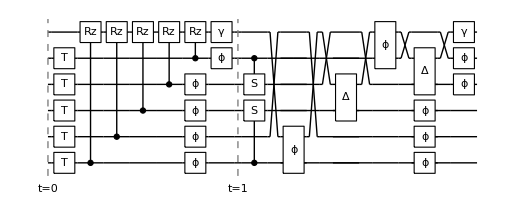

```mathematica
DrawCircuit @ InsertCircuitNoise[in, myDevSpec]
```

A user input circuit cannot make use of the hidden qubit.

```mathematica
InsertCircuitNoise[Circuit[ Subscript[T, 5] ], myDevSpec]
```

InsertCircuitNoise::error: The given subcircuits contain gates not supported by the given device specification. See ?GetUnsupportedGates.

$Failed